```mathematica
(*Práctica 2.2 CMC
II- Reconocedores de lenguaje

Ángel Carrascosa Beltrán
Laura Ruiz Muñoz*)


(*AC=(S,f,S+)
	S=estados -> S- U S+
   f={transiciones} : transicion={valorCeldaVecinaIzq,ValorCeldaAct,ValorCeldaNuevo}[Unidireccional] | transicion={valorCeldaVecinaIzq,ValorCeldaAct,valorCeldaVecinaDcha,ValorCeldaNuevo}[Unidireccional]
 S+=estados aceptacion
 S-=estados rechazo
*)
(*ADF={{estados},{alfabeto},{transiciones},estadoInicial,{estadosFinales}
transicion={estadoActual,simbolo,estadoNuevo}*)

(*Ejercicio1*)

(* Combinaciones de vecindarios posibles
(letra,letra) Si, 1;
(estado,letra) Si, 3; transiciones ADF;
(estado,estado) Si, 2;
(letra,estado) No;
*)

ADFtoACUnidireccional[ADF_]:=Module[{transiciones,estados,alfabeto,estadosFinales,ac,ACtrans,ACestados,i,j},
transiciones=ADF[[3]];
estados=ADF[[1]];
alfabeto=ADF[[2]];
estadosFinales=ADF[[5]];
ACtrans=transiciones;
ACestados=Join[alfabeto,estados];
For[i=1,i≤ Length[alfabeto],i++,
For[j=1,j≤Length[alfabeto],j++,
ACtrans=Append[ACtrans,{alfabeto[[j]],alfabeto[[i]],alfabeto[[i]]}];
];
];
For[i=1,i≤ Length[estados],i++,
For[j=1,j≤Length[estados],j++,
ACtrans=Append[ACtrans,{estados[[j]],estados[[i]],estados[[i]]}];
];
];
For[i=1,i≤ Length[alfabeto],i++,
For[j=1,j≤Length[estados],j++,
If[Not[MemberQ[ACtrans,{estados[[j]],alfabeto[[i]],_}]],
ACtrans=Append[ACtrans,{estados[[j]],alfabeto[[i]],alfabeto[[i]]}];
];
];
];
ac={ACestados,ACtrans,estadosFinales};
Return[ac];
];

ADFtoACUnidireccional[{{Q,P,R},{a,b},{{Q,a,P},{Q,b,R},{P,a,R},{P,b,Q},{R,a,R},{R,b,R}},Q,{R}}]
```

{{a,b,Q,P,R},{{Q,a,P},{Q,b,R},{P,a,R},{P,b,Q},{R,a,R},{R,b,R},{a,a,a},{b,a,a},{a,b,b},{b,b,b},{Q,Q,Q},{P,Q,Q},{R,Q,Q},{Q,P,P},{P,P,P},{R,P,P},{Q,R,R},{P,R,R},{R,R,R}},{R}}

```mathematica
(*Ejercicicio3*)

(* Combinaciones de vecindarios posibles
(letra,letra,letra) Si, 1;
 (letra,letra,estado) Si, 1;
 (estado,letra,letra) Si, 3; transiciones ADF;
 (estado,letra,estado) Si, 3; transiciones ADF;
 (estado,estado,estado) Si, 2;
 (estado,estado,letra) Si, 2;
 (letra,estado,estado) No;
 (letra,estado,letra) No;
*)

ADFtoACBidireccional[ADF_]:=Module[{transiciones,estados,alfabeto,estadosFinales,ac,ACtrans,ACestados,i,j,k,l,m},
transiciones=ADF[[3]];
estados=ADF[[1]];
alfabeto=ADF[[2]];
estadosFinales=ADF[[5]];
ACtrans={};
ACestados=Join[alfabeto,estados];
(*transaciones ADF*)
For[l=1,l≤Length[transiciones],l++,
For[m=1,m≤Length[ACestados],m++,
ACtrans=Append[ACtrans,{transiciones[[l]][[1]],transiciones[[l]][[2]],ACestados[[m]],transiciones[[l]][[3]]}];
];
];
(**)
For[i=1,i≤ Length[alfabeto],i++,
For[j=1,j≤Length[alfabeto],j++,
For[k=1,k≤Length[ACestados],k++,
ACtrans=Append[ACtrans,{alfabeto[[j]],alfabeto[[i]],ACestados[[k]],alfabeto[[i]]}];
];
];
];
For[i=1,i≤ Length[estados],i++,
For[j=1,j≤Length[estados],j++,
For[k=1,k≤Length[ACestados],k++,
ACtrans=Append[ACtrans,{estados[[j]],estados[[i]],ACestados[[k]],estados[[i]]}];
];
];
];
For[i=1,i≤ Length[alfabeto],i++,
For[j=1,j≤Length[estados],j++,
For[k=1,k≤Length[ACestados],k++,
If[Not[MemberQ[ACtrans,{estados[[j]],alfabeto[[i]],ACestados[[k]],_}]],
ACtrans=Append[ACtrans,{estados[[j]],alfabeto[[i]],ACestados[[k]],alfabeto[[i]]}];
];
];
];
];
ac={ACestados,ACtrans,estadosFinales};
Return[ac];
];
ADFtoACBidireccional[{{Q,P,R},{a,b},{{Q,a,P},{Q,b,R},{P,a,R},{P,b,Q},{R,a,R},{R,b,R}},Q,{R}}]
```

{{a,b,Q,P,R},{{Q,a,a,P},{Q,a,b,P},{Q,a,Q,P},{Q,a,P,P},{Q,a,R,P},{Q,b,a,R},{Q,b,b,R},{Q,b,Q,R},{Q,b,P,R},{Q,b,R,R},{P,a,a,R},{P,a,b,R},{P,a,Q,R},{P,a,P,R},{P,a,R,R},{P,b,a,Q},{P,b,b,Q},{P,b,Q,Q},{P,b,P,Q},{P,b,R,Q},{R,a,a,R},{R,a,b,R},{R,a,Q,R},{R,a,P,R},{R,a,R,R},{R,b,a,R},{R,b,b,R},{R,b,Q,R},{R,b,P,R},{R,b,R,R},{a,a,a,a},{a,a,b,a},{a,a,Q,a},{a,a,P,a},{a,a,R,a},{b,a,a,a},{b,a,b,a},{b,a,Q,a},{b,a,P,a},{b,a,R,a},{a,b,a,b},{a,b,b,b},{a,b,Q,b},{a,b,P,b},{a,b,R,b},{b,b,a,b},{b,b,b,b},{b,b,Q,b},{b,b,P,b},{b,b,R,b},{Q,Q,a,Q},{Q,Q,b,Q},{Q,Q,Q,Q},{Q,Q,P,Q},{Q,Q,R,Q},{P,Q,a,Q},{P,Q,b,Q},{P,Q,Q,Q},{P,Q,P,Q},{P,Q,R,Q},{R,Q,a,Q},{R,Q,b,Q},{R,Q,Q,Q},{R,Q,P,Q},{R,Q,R,Q},{Q,P,a,P},{Q,P,b,P},{Q,P,Q,P},{Q,P,P,P},{Q,P,R,P},{P,P,a,P},{P,P,b,P},{P,P,Q,P},{P,P,P,P},{P,P,R,P},{R,P,a,P},{R,P,b,P},{R,P,Q,P},{R,P,P,P},{R,P,R,P},{Q,R,a,R},{Q,R,b,R},{Q,R,Q,R},{Q,R,P,R},{Q,R,R,R},{P,R,a,R},{P,R,b,R},{P,R,Q,R},{P,R,P,R},{P,R,R,R},{R,R,a,R},{R,R,b,R},{R,R,Q,R},{R,R,P,R},{R,R,R,R}},{R}}

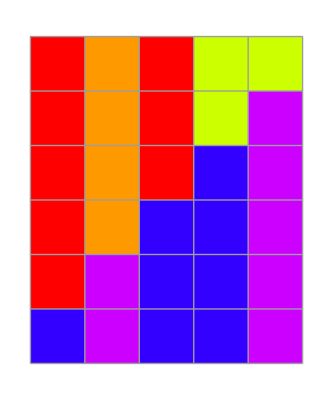

```mathematica
(*El módulo de a continuación va dentro del módulo del ejercicio 4 y el ejercicio 2, que son "ACExec" y "ACComprobarCadena" respectivamente*)

NextTransition[trans0_List,rule_List,frontierState_]:=Module[{transAct,transRes,cellNeigborhood,i,x},
transRes={};
transAct=Append[trans0,frontierState];
transAct=Prepend[transAct,frontierState];
For[i=2,i<Length[transAct],i++,
cellNeigborhood={transAct[[i-1]],transAct[[i]],_};
x=Cases[rule,cellNeigborhood];
If[Length[x]>0,
transRes=Append[transRes,x[[1]][[3]]];
,(*else*)
transRes=Append[transRes,transAct[[i]]];
];
];
Return[transRes];
];
(*Ejercicio 4*)

ACExec[Inicial_List,AC_List,frontierState_]:=Module[{transitions,ruleList,i,Splus,Sminus,colorMap,j,simb,ACStates,estados},
If[Length[Inicial]<1,
Return[False]
];
transitions={Inicial};
ACStates=AC[[1]];
ruleList=AC[[2]];
For[i=1,i<=Length[Inicial],i++,
transitions=Append[transitions,NextTransition[transitions[[Length[transitions]]],ruleList,frontierState]];
];
(**)
For[i=1,i≤Length[transitions],i++,
For[j=1,j≤Length[transitions[[1]]],j++,
transitions[[i]][[j]]=ToCharacterCode[ToString[transitions[[i]][[j]]]]/10;
];
];
(**)
ArrayPlot[transitions,ColorFunction->Hue,Mesh->True,DataReversed->True]
];
ACExec[{a,b,a,a,b},ADFtoACUnidireccional[{{Q,P,R},{a,b,c,d,e,a,b,c,d,e,a,c},{{Q,a,P},{Q,b,R},{P,a,R},{P,b,Q},{R,a,R},{R,b,R}},Q,{R}}],Q]
```

```mathematica
(*Ejercicio 2*)

ACComprobarCadena[Inicial_List,AC_List,frontierState_]:=Module[{actTransAC,ruleList,i,Splus,Sminus,colorRule},
If[Length[Inicial]<1,
Return[False](*?*)
];
actTransAC=Inicial;
Splus=AC[[3]];
ruleList=AC[[2]];
For[i=1,i<=Length[Inicial],i++,
actTransAC=NextTransition[actTransAC,ruleList,frontierState];
];
If[MemberQ[Splus,actTransAC[[Length[actTransAC]]]],Return[True];];
Return[False];
];

ACComprobarCadena[{a,b,a,a,b},ADFtoACUnidireccional[{{Q,P,R},{a,b},{{Q,a,P},{Q,b,R},{P,a,R},{P,b,Q},{R,a,R},{R,b,R}},Q,{R}}],Q]
```

True